## 2D AFHM: L = 4, N = 16

```mathematica
Remove["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Energies = Flatten[Import["energies2d.mat"]];
```

```mathematica
(*choose broadening width*)sigma=0.1;
(*pick a fine grid over the energy range*)
energyGrid=Subdivide[Min[Energies],Max[Energies]+3 sigma,200];
```

```mathematica
(*original strong B/G/R palette*)paletteBGR={RGBColor[31/255,119/255,180/255],(*strong blue*)RGBColor[44/255,160/255,44/255],(*strong green*)RGBColor[214/255,39/255,40/255]    (*strong red*)};

(*darkening factor*)
darkFactor=0.95;

(*produce a darker version*)
palette=paletteBGR/. RGBColor[r_,g_,b_]:>RGBColor[darkFactor*r,darkFactor*g,darkFactor*b];
```

## FirstBlockPredictedShift

```mathematica
probs = Flatten[Import["pred_shift_2d_D50_probs.mat"]];
rho[x_]:=Total[probs*Table[(1/(sigma Sqrt[2 Pi]))Exp[-(x-En)^2/(2 sigma^2)],{En,Energies}]];
SmoothedProbs = Table[rho[En],{En,energyGrid}];
datapredshift1=Transpose@{energyGrid-Min[Energies],Log10[SmoothedProbs]};
```

General::munfl: Exp[-720.434] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

## SecondBlockPredictedShift

```mathematica
probs = Flatten[Import["pred_shift_2d_D100_probs.mat"]];
rho[x_]:=Total[probs*Table[(1/(sigma Sqrt[2 Pi]))Exp[-(x-En)^2/(2 sigma^2)],{En,Energies}]];
SmoothedProbs = Table[rho[En],{En,energyGrid}];
datapredshift2=Transpose@{energyGrid-Min[Energies],Log10[SmoothedProbs]};
```

General::munfl: Exp[-720.434] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

## ThirdBlockPredictedShift

```mathematica
probs = Flatten[Import["pred_shift_2d_D150_probs.mat"]];
rho[x_]:=Total[probs*Table[(1/(sigma Sqrt[2 Pi]))Exp[-(x-En)^2/(2 sigma^2)],{En,Energies}]];
SmoothedProbs = Table[rho[En],{En,energyGrid}];
datapredshift3=Transpose@{energyGrid-Min[Energies],Log10[SmoothedProbs]};
```

General::munfl: Exp[-720.434] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

## FirstBlockPredicted

```mathematica
probs = Flatten[Import["pred_2d_D50_noconserve_probs.mat"]];
rho[x_]:=Total[probs*Table[(1/(sigma Sqrt[2 Pi]))Exp[-(x-En)^2/(2 sigma^2)],{En,Energies}]];
SmoothedProbs = Table[rho[En],{En,energyGrid}];
datapred1=Transpose@{energyGrid-Min[Energies],Log10[SmoothedProbs]};
```

## SecondBlockPredicted

```mathematica
probs = Flatten[Import["pred_2d_D100_noconserve_probs.mat"]];
rho[x_]:=Total[probs*Table[(1/(sigma Sqrt[2 Pi]))Exp[-(x-En)^2/(2 sigma^2)],{En,Energies}]];
SmoothedProbs = Table[rho[En],{En,energyGrid}];
datapred2=Transpose@{energyGrid-Min[Energies],Log10[SmoothedProbs]};
```

General::munfl: Exp[-720.434] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

## ThirdBlockPredicted

```mathematica
probs = Flatten[Import["pred_2d_D150_noconserve_probs.mat"]];
rho[x_]:=Total[probs*Table[(1/(sigma Sqrt[2 Pi]))Exp[-(x-En)^2/(2 sigma^2)],{En,Energies}]];
SmoothedProbs = Table[rho[En],{En,energyGrid}];
datapred3=Transpose@{energyGrid-Min[Energies],Log10[SmoothedProbs]};
```

General::munfl: Exp[-720.434] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

## FirstBlockActual

```mathematica
probs = Flatten[Import["psi0_2d_D50_noconserve_probs.mat"]];
rho[x_]:=Total[probs*Table[(1/(sigma Sqrt[2 Pi]))Exp[-(x-En)^2/(2 sigma^2)],{En,Energies}]];
SmoothedProbs = Table[rho[En],{En,energyGrid}];
actdata1=Transpose@{energyGrid-Min[Energies],Log10[SmoothedProbs]};
```

General::munfl: Exp[-720.434] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

## SecondBlockActual

```mathematica
probs = Flatten[Import["psi0_2d_D100_noconserve_probs.mat"]];
rho[x_]:=Total[probs*Table[(1/(sigma Sqrt[2 Pi]))Exp[-(x-En)^2/(2 sigma^2)],{En,Energies}]];
SmoothedProbs = Table[rho[En],{En,energyGrid}];
actdata2=Transpose@{energyGrid-Min[Energies],Log10[SmoothedProbs]};
```

General::munfl: Exp[-720.434] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

## ThirdBlockActual

```mathematica
probs = Flatten[Import["psi0_2d_D150_noconserve_probs.mat"]];
rho[x_]:=Total[probs*Table[(1/(sigma Sqrt[2 Pi]))Exp[-(x-En)^2/(2 sigma^2)],{En,Energies}]];
SmoothedProbs = Table[rho[En],{En,energyGrid}];
actdata3=Transpose@{energyGrid-Min[Energies],Log10[SmoothedProbs]};
```

## MakePlot D=50

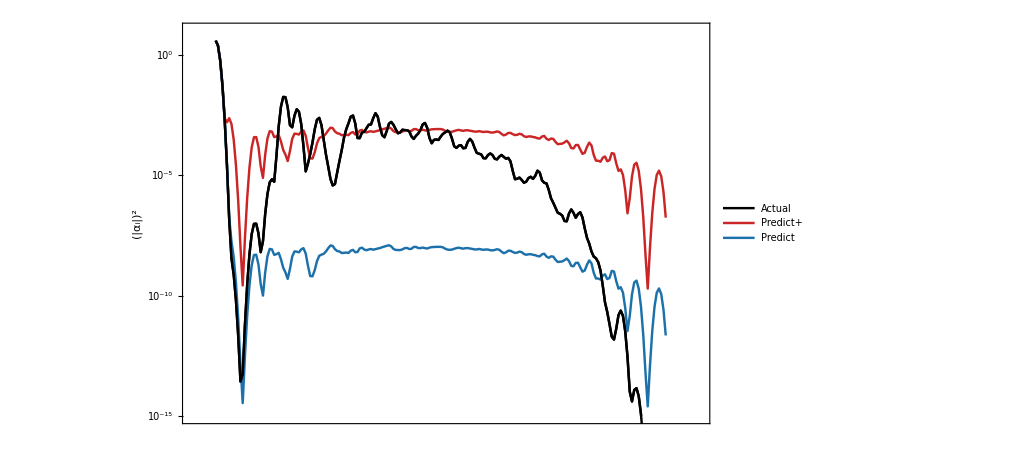

```mathematica
tickLen={0.015,0};
ymin = - 16;
ymax=0;
yTicks=Table[{i,Superscript[10,i],tickLen},{i,-15,0,5}];
xTicks=Table[{i,"",tickLen},{i,0,20,5}];
xTicksAbove=Table[{i,"",tickLen},{i,0,15,5}];
yTicksRight = Table[{i,"",tickLen},{i,-15,-10,5}];

imgSize=750;
imagePadding={{120,10},{120,10}};

plot50=ListLinePlot[{actdata1,datapredshift1,datapred1},
PlotStyle->{{Black,AbsoluteThickness[1.75]},{palette[[3]],AbsoluteThickness[1.75]},{palette[[1]],AbsoluteThickness[1.75]}},
Frame->True,
FrameStyle->Directive[Black,AbsoluteThickness[2]],
Axes->False,
FrameTicks->{{yTicks,yTicksRight},{xTicks,xTicksAbove}},
FrameTicksStyle->Directive[AbsoluteThickness[2]],
FrameLabel->{{TraditionalForm[Superscript[Row[{"|",Subscript[α,i],"|"}],2]],None},{None,None}},LabelStyle->{FontFamily->"Times",FontSize->30},
PlotRange->{{-1,21},{-15,1}},
PlotTheme->"Detailed",
GridLines->None,
PlotLegends->Placed[LineLegend[{"Actual","Predict+" , "Predict"},LegendFunction->(Framed[#,Background->White,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameMargins->{{8,15},{0,8}}]&),LegendMarkerSize->20,LegendLayout->"Column",LabelStyle->{FontFamily->"Times",FontSize->20}],Scaled[{0.91,0.85}]],
ImageSize->imgSize,ImagePadding->imagePadding,
Epilog->{Black,AbsoluteThickness[1.75],Line[actdata1]}
(*,Epilog->{AbsoluteThickness[1],Black,Line[{{1.71079522449159,ymin},{1.71079522449159,ymax}}]}*)
]
```

```mathematica
(*Export["2d_spectra_D50.pdf",plot50,"pdf"]*)
```

## MakePlot D=100

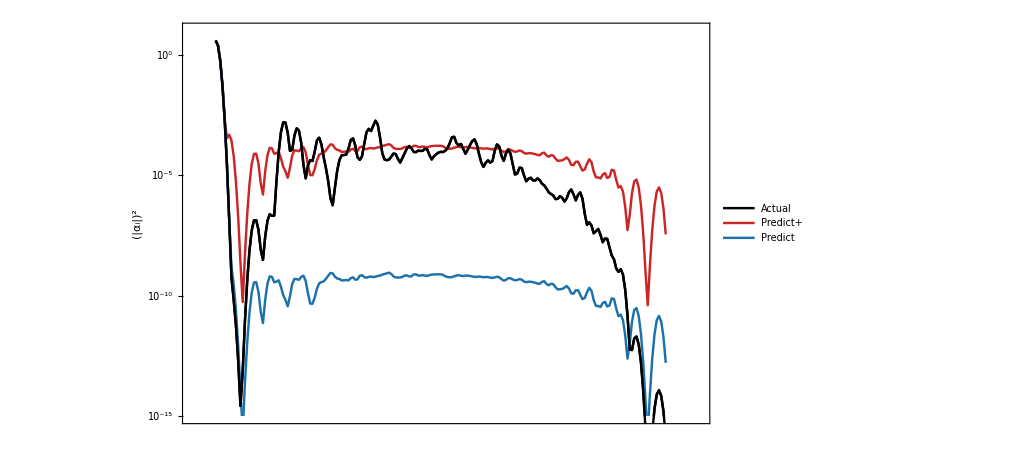

```mathematica
tickLen={0.015,0};
ymin = - 16;
ymax=0;
yTicks=Table[{i,Superscript[10,i],tickLen},{i,-15,0,5}];
xTicks=Table[{i,"",tickLen},{i,0,20,5}];
xTicksAbove=Table[{i,"",tickLen},{i,0,15,5}];
yTicksRight = Table[{i,"",tickLen},{i,-15,-10,5}];

imgSize=750;
imagePadding={{120,10},{120,10}};

plot100=ListLinePlot[{actdata2,datapredshift2,datapred2},
PlotStyle->{{Black,AbsoluteThickness[1.75]},{palette[[3]],AbsoluteThickness[1.75]},{palette[[1]],AbsoluteThickness[1.75]}},
Frame->True,
FrameStyle->Directive[Black,AbsoluteThickness[2]],
Axes->False,
FrameTicks->{{yTicks,yTicksRight},{xTicks,xTicksAbove}},
FrameTicksStyle->Directive[AbsoluteThickness[2]],
FrameLabel->{{TraditionalForm[Superscript[Row[{"|",Subscript[α,i],"|"}],2]],None},{None,None}},LabelStyle->{FontFamily->"Times",FontSize->30},
PlotRange->{{-1,21},{-15,1}},
PlotTheme->"Detailed",
GridLines->None,
PlotLegends->Placed[LineLegend[{"Actual","Predict+" , "Predict"},LegendFunction->(Framed[#,Background->White,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameMargins->{{8,15},{0,8}}]&),LegendMarkerSize->20,LegendLayout->"Column",LabelStyle->{FontFamily->"Times",FontSize->20}],Scaled[{0.91,0.85}]],
ImageSize->imgSize,ImagePadding->imagePadding,
Epilog->{Black,AbsoluteThickness[1.75],Line[actdata2]}
(*,Epilog->{AbsoluteThickness[1],Black,Line[{{1.71079522449159,ymin},{1.71079522449159,ymax}}]}*)
]
```

```mathematica
(*Export["2d_spectra_D100.pdf",plot100,"pdf"]*)
```

## MakePlot D=150

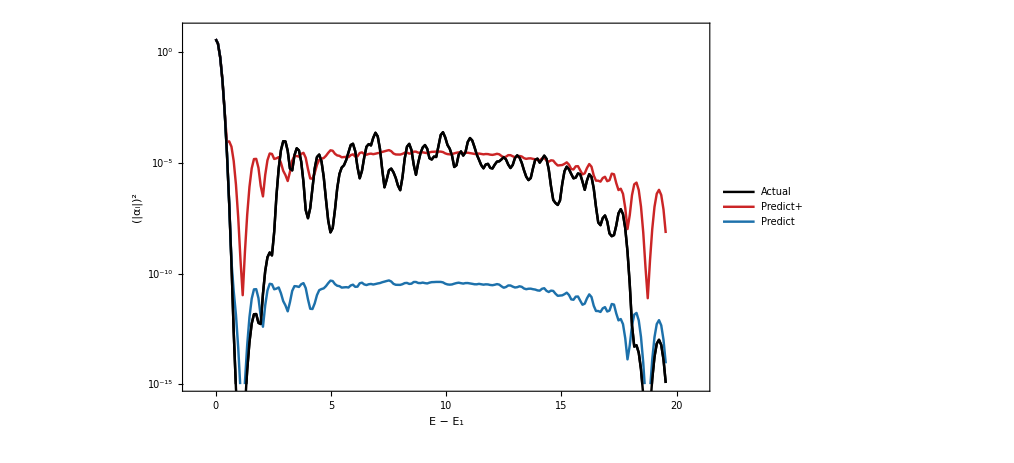

```mathematica
(*ymin=Floor[Min[data1[[All,2]]]];*)
tickLen={0.015,0};
ymin = - 16;
ymax=0;
yTicks=Table[{i,Superscript[10,i],tickLen},{i,-15,0,5}];
xTicks=Table[{i,i,tickLen},{i,0,20,5}];
xTicksAbove=Table[{i,"",tickLen},{i,0,15,5}];
yTicksRight = Table[{i,"",tickLen},{i,-15,-10,5}];

imgSize=750;
imagePadding={{120,10},{120,10}};

plot150=ListLinePlot[{actdata3,datapredshift3,datapred3},
PlotStyle->{{Black,AbsoluteThickness[1.75]},{palette[[3]],AbsoluteThickness[1.75]},{palette[[1]],AbsoluteThickness[1.75]}},
Frame->True,
FrameStyle->Directive[Black,AbsoluteThickness[2]],
Axes->False,
FrameTicks->{{yTicks,yTicksRight},{xTicks,xTicksAbove}},
FrameTicksStyle->Directive[AbsoluteThickness[2]],
FrameLabel->{{TraditionalForm[Superscript[Row[{"|",Subscript[α,i],"|"}],2]],None},{TraditionalForm[Row[{"E"," − ",Subscript["E",1]}]],None}},
LabelStyle->{FontFamily->"Times",FontSize->30},LabelStyle->{FontFamily->"Times",FontSize->30},
PlotRange->{{-1,21},{-15,1}},
PlotTheme->"Detailed",
GridLines->None,
PlotLegends->Placed[LineLegend[{ "Actual", "Predict+","Predict"},LegendFunction->(Framed[#,Background->White,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameMargins->{{8,15},{0,8}}]&),LegendMarkerSize->20,LegendLayout->"Column",LabelStyle->{FontFamily->"Times",FontSize->20}],Scaled[{0.91,0.85}]],
ImageSize->imgSize,ImagePadding->imagePadding,
Epilog->{Black,AbsoluteThickness[1.75],Line[actdata3]}
(*,Epilog->{AbsoluteThickness[1],Black,Line[{{1.71079522449159,ymin},{1.71079522449159,ymax}}]}*)
]
```

```mathematica
(*Export["2d_spectra_D150.pdf",plot150,"pdf"]*)
```